# Majorana stars figure in spin-1

### Pauli spin matrices

```mathematica
Fx = 1/(√2)({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}});
Fy=I/(√2)({{0, -1, 0}, {1, 0, -1}, {0, 1, 0}});
Fz=({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
```

### Define function which produces figure of Majorana stars

```mathematica
Majoranastars[ψ0_]:=
Module[{ψ=ψ0,normψ, ys, P, solution, ϕ,θ, angle, coor, stereopoints,stero, state,arrow1,arrow2,arrow3,a,numbcircs, numblines, circ, lines,BlochSphere,BLsphereCoors,avgF,axesLabels,sphere},
normψ = ψ/Norm[ψ];

(*Check element is zero otherwise divergence will occur*)

If[normψ[[1,1]]==0,
normψ[[1,1]]=10^-10];
ys= Flatten[Conjugate[normψ],1];

(*Polynomial form*)
P[z_]:=#[[3]]+#[[2]]*√2*z+#[[1]]*z^2&@normψ;

(*Find the roots and locations of the stars*)
solution =Solve[P[z]==0,z];
ϕ =Extract[Arg[solution[[;;,;;,2]]],{All,1}];
θ =Extract[2*ArcTan[Abs[solution[[;;,;;,2]]]],{All,1}];
angle={Cos[#],Sin[#]}&/@ϕ;

(*coordinate of the stars on the sterograph*)
coor =angle*θ//MatrixForm;
stereopoints =ListPlot[{coor[[1,1]],coor[[1,2]]},PlotStyle->{PointSize[0.02],Red}];

(*Pauli state*)
state = Flatten[{ys.Fx.normψ,ys.Fy.normψ,ys.Fz.normψ},2]//N;
arrow3 =Graphics3D[{Black,Thick,Arrow[{{0,0,0},state}]}];

(*Create sterograph*)
a =√(π^2/2);
numbcircs = {π/4,π/2,3π/4,π};
numblines = Permutations[{a,-a,a,-a,a,a,-a,-a},{2}];
circ = Graphics[Circle[{0,0},# ]&/@numbcircs];
lines = Graphics[Line[{{0,0},#}]&/@numblines,Axes->True,Ticks->{numbcircs},AxesLabel->{"θ", "ϕ = π/2"},LabelStyle->Directive[Blue,Bold]];
stero=Show[{lines,circ,stereopoints},ImageSize-> {350}];

(*Map to Bloch (Riemann sphere)*);
SetOptions[ParametricPlot3D,PlotStyle->Opacity[0.05]
];
BlochSphere=ParametricPlot3D[
{Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]},
{ϕ,0,2π},
{θ,0,π},MeshStyle->{{Opacity[0.2],Black},{Opacity[0.2],Black}}
];
BLsphereCoors = {Cos[#1]*Sin[#2],Sin[#1]*Sin[#2],Cos[#2]}&[ϕ,θ];
arrow1 = Graphics3D[{Red,Thick,Arrow[Tube[{{0,0,0},BLsphereCoors[[;;,1]]}]]}];
arrow2 = Graphics3D[{Red,Thick,Arrow[Tube[{{0,0,0},BLsphereCoors[[;;,2]]}]]}]; 
avgF= 2*Table[Sum[BLsphereCoors[[j,i]],{i,1,2}],{j,1,3}]/(3+Flatten[BLsphereCoors[[;;,2]],1].Flatten[BLsphereCoors[[;;,1]],1]);
arrow3=Graphics3D[{Blue,Thick,Arrow[Tube[{{0,0,0},avgF}]]}];
axesLabels=Style[#,Black,Bold,FontSize->20]&/@{"⟨F_x⟩","⟨F_z⟩","⟨F_y⟩"};
sphere = Show[{{BlochSphere,arrow1,arrow2}},AxesStyle->Thick,AxesOrigin-> {0,0,0},ImageSize-> {700},Boxed->False,Ticks->{{{1,"⟨F_x⟩"},None},{{1,"⟨F_y⟩"},None},{{1,"⟨F_z⟩"},None}},TicksStyle->Directive[Black, Bold, Italic,14],ImageResolution-> {1000},ViewPoint->{1.3, -2.4, 1}];

ArcCos[(BLsphereCoors[[;;,1]].BLsphereCoors[[;;,2]])/(Norm[BLsphereCoors[[;;,1]]]Norm[BLsphereCoors[[;;,1]]])]
]
```

```mathematica
angleVsqR=Table[
H = Fx+qR*Fz.Fz;
Eigs = Eigenvectors[H];
eigstars = Map[{#}&,Eigs,{2}];
ϕlist=Map[Majoranastars,eigstars];
{qR,ϕlist[[1]]/π},
{qR,0,3*0.348,0.1*0.348}
]
```

{{0.,0.},{0.0348,0.118413},{0.0696,0.166963},{0.1044,0.203868},{0.1392,0.234682},{0.174,0.261562},{0.2088,0.285617},{0.2436,0.307508},{0.2784,0.327666},{0.3132,0.346392},{0.348,0.363905},{0.3828,0.380372},{0.4176,0.395921},{0.4524,0.410658},{0.4872,0.424665},{0.522,0.438013},{0.5568,0.45076},{0.5916,0.462957},{0.6264,0.474646},{0.6612,0.485865},{0.696,0.496646},{0.7308,0.507019},{0.7656,0.517009},{0.8004,0.52664},{0.8352,0.535931},{0.87,0.544902},{0.9048,0.553571},{0.9396,0.561952},{0.9744,0.57006},{1.0092,0.577909},{1.044,0.585511}}

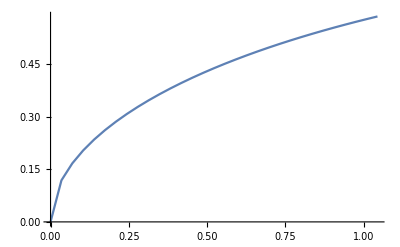

```mathematica
ListPlot[angleVsqR,Joined->True,PlotRange->{0,All}]
```

```mathematica
angleVsqR[[11]]
```

{0.348,0.363905}

```mathematica
e1-e2
e3-e2
e1-e3
```

{{2},{-√2},{0}}

{{2},{√2},{0}}

{{0},{-2 √2},{0}}

```mathematica
stars1={{-0.8410251228417943,-0.8410251228417943},{-0.5409960653728868,0.5409960653728868},{2.83276944882399*^-16,2.83276944882399*^-16}};
```

```mathematica
ArcCos[(stars1[[;;,1]].stars1[[;;,2]])/(Norm[stars1[[;;,1]]]Norm[stars1[[;;,1]]])]
```

0.363905